### More inputs and outputs: no improvement

20 inputs and outputs for k = 3

```mathematica
dubevosk32 = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 20}]], 2]&)|>], {j, 60}];
```

```mathematica
Iconize[dubevosk32];
```

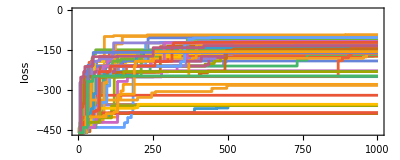

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ dubevosk32, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4]
```

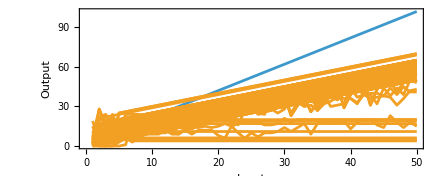

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&/@ dubevosk32[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

### Evolving just based on the width of the output

```mathematica
dubevosk33 = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[Table[Length[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] -  2i+2, {i, 5}]]]&)|>], {j, 60}];
```

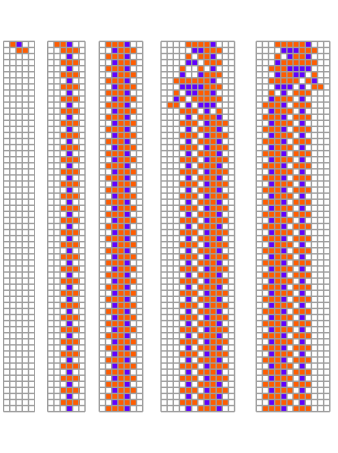

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#, 1]&/@#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, Mesh->True]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&[MaximalBy[dubevosk33, #[[-1, "Fitness"]]&, 1][[1, -1]]]]
```

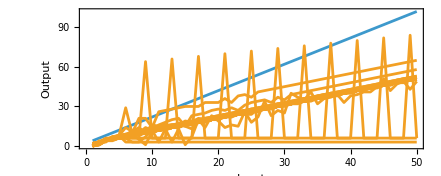

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Length/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&/@ dubevosk33[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

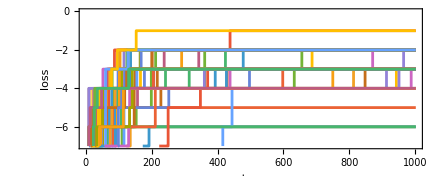

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ dubevosk33, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4]
```

### Testing rule mutation specs

```mathematica
ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 4, 1}, "Depth"->2, 
"MutationFunction"->1,
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {j, 1}]
```

{{<|Rule→{0,4,1},Fitness→-40|>,<|Rule→{18446744073709551616,4,1},Fitness→-40|>,<|Rule→{18518801667747479552,4,1},Fitness→-40|>}}

```mathematica
ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 4, 1}, "Depth"->2, 
"MutationFunction"->1,
 "FitnessFunction"-> "Lifetime"|>], {j, 1}]
```

### ArrayPatchFrequencyChart

#### v1

```mathematica
k5evos = ;
```

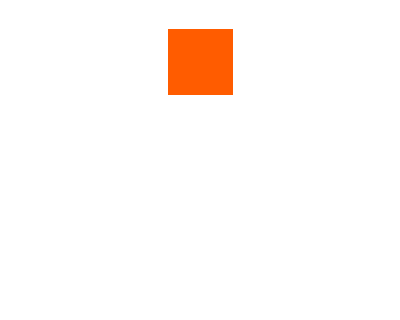
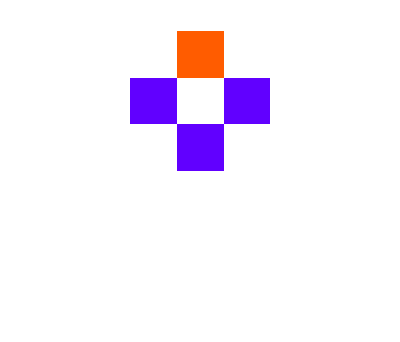
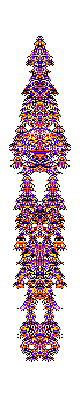
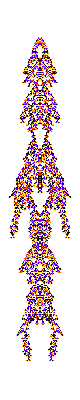
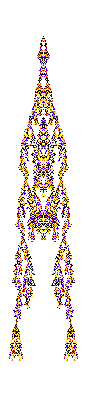
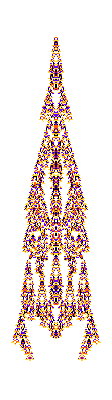
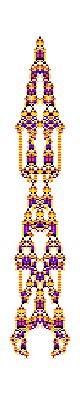
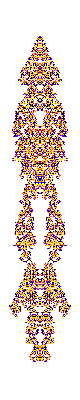
{-Graphics-1,-Graphics-3,-Graphics-764,-Graphics-677,-Graphics-958,-Graphics-1,-Graphics-490,-Graphics-246,-Graphics-972,-Graphics-923,-Graphics-999,-Graphics-797,-Graphics-550,-Graphics-999,-Graphics-839,-Graphics-837,-Graphics-212,-Graphics-497,-Graphics-1,-Graphics-117,-Graphics-987,-Graphics-377,-Graphics-387,-Graphics-897,-Graphics-3,-Graphics-945,-Graphics-980,-Graphics-424,-Graphics-2,-Graphics-1,-Graphics-514,-Graphics-957,-Graphics-773,-Graphics-836,-Graphics-1,-Graphics-936,-Graphics-538,-Graphics-1,-Graphics-507,-Graphics-842,-Graphics-755,-Graphics-978,-Graphics-939,-Graphics-982,-Graphics-1,-Graphics-5,-Graphics-964,-Graphics-1,-Graphics-359,-Graphics-915}

```mathematica
Module[{data,res},
res=Map[CompoundExpression[
data=CellularAutomaton[
#[[1]],{{1},0},#[[2]]+2],
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,17Sqrt[Length[data]+1]}
],Style[#[[2]],"Text",Italic,Gray,11]]]&,
k5evos];
Style[res,LineSpacing->{1.2,0}]
]
```

```mathematica
Position[,-Graphics-]
```

{{1,27,1}}

```mathematica
Position[,-Graphics-]
```

{{1,8,1}}

```mathematica
Position[,-Graphics-]
```

{{1,16,1}}

```mathematica
k5evos[[{8, 16, 27}]]
```

{{{1843702513142487328663954627093956123917772641192902420550524030507797003275769629122575,5,1},246},{{687377017085252560711205570056448172607101199239134331323563847951884759769294147818775,5,1},837},{{216685517436460172513340208393391909630025373855861162840748357671300356130878056881485,5,1},980}}

```mathematica
ArrayPlot[CellularAutomaton[#1, {{1}, 0}, 1000], ColorRules->colorrules, ImageSize->{Automatic, 800}]&@@@k5evos[[{8, 16, 27}]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Part[]
```

```mathematica
ClearAll[ArrayPatchFrequencyChart];
Options[ArrayPatchFrequencyChart]= {"ShowSequences"->True, "SequenceSize"->{30, 30}};
ArrayPatchFrequencyChart[arr_, blockspec_,offsetspec_, n_:10, OptionsPattern[{ArrayPatchFrequencyChart, BarChart}]]:= Module[{},
counts = ReverseSort[Counts[Catenate[Partition[arr,blockspec, offsetspec]]]][[If[ListQ[n], First[n], 1];;If[ListQ[n], Last[n], n]]];
labfunc = If[OptionValue["ShowSequences"], (Placed[ArrayPlot[Keys[counts][[#2[[2]]]], ImageSize->OptionValue["SequenceSize"], ColorRules->colorrules, Mesh->True],Below]&), Automatic];
BarChart[Values[counts], LabelingFunction-> labfunc,ScalingFunctions-> OptionValue[ScalingFunctions]]
]
```

```mathematica
counts
```

```mathematica
counts
```

<|{{0,0,0},{0,0,0},{0,0,0}}→1674,{{0,0,1},{0,0,3},{0,0,1}}→66,{{1,0,0},{3,0,0},{1,0,0}}→66,{{0,0,0},{0,0,1},{0,0,4}}→46,{{0,0,0},{1,0,0},{4,0,0}}→46,{{0,3,3},{0,1,1},{0,3,3}}→43,{{3,3,0},{1,1,0},{3,3,0}}→43,{{0,1,1},{0,3,3},{0,1,1}}→42,{{1,1,0},{3,3,0},{1,1,0}}→42,{{0,0,3},{0,0,1},{0,0,3}}→42|>

```mathematica
GraphicsGrid[Partition[MapIndexed[BarChart[ReplacePart[#,10->Callout[#[[10]],PlotCA[l1[[bmi[[#2[[1]]]],1]],"Trim"->{1,3}],Above,Appearance->None]],PlotRange->100,Frame->True,FrameTicks->{{If[#2[[1]]==1||#2[[1]]==4,Automatic,None],Automatic},{If[4<=#2[[1]]<=6,Table[{i,5i},{i,0,50,10}],None],Automatic}},BarSpacing->None,ImageSize->{If[#2[[1]]==1||#2[[1]]==4,285,280],Automatic},LabelingSize->100,PlotRange->150,PlotRangePadding->{Automatic,0},Epilog->{Dotted,Red,Line[{{means[[bmi[[#2[[1]]]]]]/5,100},{means[[bmi[[#2[[1]]]]]]/5,0}}]}]&,MapAt[Style[#,Red]&,BinCounts[#,{5}]&/@(samplts[[bmi[[;;6]]]]/.-Infinity->210),{All,-1}]],3],Spacings->0,ImageSize->{600,Automatic}]
```

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 200], {3, 3}, {1, 1},{2, All}, "ShowSequences"->False,"SequenceSize"->{5, 5}, ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[k5evos[[16, 1]], {{1}, 0}, 200], {3, 3}, {1, 1},{2, All}, "ShowSequences"->False,"SequenceSize"->{5, 5}, ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 200], {3, 3}, {1, 1},{2, All}, "ShowSequences"->False,"SequenceSize"->{5, 5}, ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[k5evos[[16, 1]], {{1}, 0}, 200], {3, 3}, {1, 1},{2, All}, "ShowSequences"->False,"SequenceSize"->{5, 5}]
```

```mathematica
BarChart[Values[ReverseSort[counts], LabelingFunction-> labfunc]]
```

```mathematica
Length[k5evos]
```

50

```mathematica
#[[1]]&/@k5evos[[;;1]]
```

{{1668212734402773202673108502102160960503298732745839559081361456200610254365998065221100,5,1}}

```mathematica
ParallelMap[ArrayPatchFrequencyChart[CellularAutomaton[#[[1]], {{1}, 0}, 200], {3, 3}, {1, 1},All, "ShowSequences"->False, ScalingFunctions->"Log"]&, k5evos]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[Values[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]&/@ Select[k5evos, Last[#] >100&], PlotRange->All, ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
ListLinePlot3D[Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&], PlotRange->All, ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
ListLinePlot3D[SortBy[Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&], Entropy], PlotRange->All, ScalingFunctions->"Log"]
```

-Graphics3D-

```mathematica
MapIndexed[#2&, {{1, 2, 3, 4}, {1, 2, 3, 4}}, {2}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}}}

```mathematica
ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, SortBy[Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&], Entropy], {2}] ]]
```

-Graphics3D-

```mathematica
ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, SortBy[Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&], Entropy], {2}]], ScalingFunctions->"Log"]
```

```mathematica
ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, SortBy[Values[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]&/@ Select[k5evos, Last[#] >100&][[;;3]], Entropy], {2}] ]]
```

-Graphics3D-

```mathematica
Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&]
```

```mathematica
ListPlot3D[Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&], PlotRange->All, ScalingFunctions->"Log"]
```

ListPlot3D::arrayerr: {{4.077537443905719,4.077537443905719,3.49650756146648,3.49650756146648,«44»,2.197224577336219,2.197224577336219,«2306»},«36»,{«59»,«49»,«2916»}} must be a valid array or a list of valid arrays.

```mathematica
ListLinePlot[Values[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]&/@ Select[k5evos, Last[#] >100&], PlotRange->All, ScalingFunctions->"Log", PlotLayout->"Stacked"]
```

-Graphics-

#### Using ListLinePlot

Looking at different block sizes

```mathematica
k5evos = ;
```

```mathematica
ArrayPlot[CellularAutomaton[#[[1]], {{1}, 0}, 200], ColorRules->colorrules]&/@ k5evos[[{8, 16, 27}]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[#[[1]], {{1}, 0}, 200], {3, 3}, {1, 1}, {2, All}, "ShowSequences"->False]&/@ k5evos[[{8, 16, 27}]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[#[[1]], {{1}, 0}, 200], {3, 3}, {1, 1}, {2, All}, "ShowSequences"->False]&/@ k5evos
```

```mathematica
ArrayPlot[CellularAutomaton[#[[1]], {{1}, 0}, 1000], ColorRules->colorrules]&/@ k5evos
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPatchFrequencyChart[CellularAutomaton[k5evos[[16, 1]], {{1}, 0}, 200], {3, 3}, {1, 1},{2, All}, "ShowSequences"->False,"SequenceSize"->{5, 5}]
```

```mathematica
Table[ListStepPlot[Rest[Values[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200], {3, 3}, {1, 1}]]]]]], PlotRange->All], {i, {8, 16, 27}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]]]&/@Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}]
```

{1229,1895,3636}

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2, ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

Normalized by number of colored cells

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2, ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2[[;;TestCALifetime[#2] + 1]], ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

```mathematica
ListPlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2[[;;TestCALifetime[#2] + 1]], ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Callout[#1,ArrayPlot[#2, ColorRules->colorrules, ImageSize->{Automatic, 80}], Scaled[.6]]&,{zs, cas}]], LabelingSize->{100, Automatic}]
```

-Graphics-

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapAt[Callout[#, ArrayPlot[cas[[1]], ColorRules->colorrules]]&,cs, {1, 1000}]
]]
```

-Graphics-

```mathematica
Table[ListLinePlot[Table[Callout[Prime[Range[20]],ArrayPlot[Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}][[1]], ColorRules->colorrules],Scaled[0.6],Frame->True,FrameMargins->i], {j, 2}]],{i,{3,6}}]
```

{-Graphics-,-Graphics-}

```mathematica
MapAt[Callout[#, ArrayPlot[Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 200],{i,{8, 16, 27}}][[1]], ColorRules->colorrules]]&,cs, {1, 1000}]
```

```mathematica
[[1, 1000]]
```

Callout[1/2525,-Graphics-]

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2, ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] &/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2, ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

#### Testing different block sizes

```mathematica
ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {3, 3}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs;
MapThread[Legended[#1,ArrayPlot[#2[[;;TestCALifetime[#2] + 1]], ColorRules->colorrules, ImageSize->{Automatic, 80}]]&,{zs, cas}]]]
```

-Graphics-

```mathematica
Table[Labeled[ListLinePlot[With[{cas = Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]},
cs = Rest[Values[ReverseSort[Counts[Catenate[Partition[#, {k, k}, {1, 1}]]]]]] / Count[#, x_/;x>0, {2}]&/@ cas;
zs  = PadRight[#, Max[Length/@ cs]]&/@ cs
], PlotTheme->"Minimal"], Text["block size: "<>ToString[{k, k}]]], {k, 2, 10}]
```

{-Graphics-block size: {2, 2},-Graphics-block size: {3, 3},-Graphics-block size: {4, 4},-Graphics-block size: {5, 5},-Graphics-block size: {6, 6},-Graphics-block size: {7, 7},-Graphics-block size: {8, 8},-Graphics-block size: {9, 9},-Graphics-block size: {10, 10}}

```mathematica
Column[Table[GraphicsRow[ArrayPatchFrequencyChart[#, {k, k}, {1, 1}, {2, 10}, "SequenceSize"->{15, 15}]&/@ Table[CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, 1000],{i,{8, 16, 27}}]], {k, 2, 10}]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

#### Normalized entropy plotted as a function of block size

```mathematica
Module[{idxs, ents, sorted},
idxs = Select[k5evos, #[[2]]>100&->"Index"];
entaps = With[{ca = CellularAutomaton[k5evos[[#, 1]], {{1}, 0}, 1000]}, {PatchEntropyNZ[ca, {3,3}], ArrayPlot[ca, ColorRules->colorrules]}]&/@idxs;
ListStepPlot[SortBy[entaps, First]]
sortedidxs = SortBy[idxs, ents[[#]]&];
Callout[ArrayPlot[CellularAutomaton[k5evos[[#, 1]], {{1}, 0}, 1000]], 



ListStepPlot[Sort[With[{ca = CellularAutomaton[#[[1]], {{1}, 0}, 1000]},Callout[,ArrayPlot[ca, ColorRules->colorrules]]]&/@ Select[k5evos, #[[2]]>100&]], LabelingSize->200]
```

-Graphics-

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropyNZ[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

-Graphics-

Non-normalized

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

-Graphics-

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropyNZ[ca, 3], #[[1]],ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},SortBy[entaps, First][[-3;;]]]
```

```mathematica
Position[k5evos[[All, 1]], {1498154354777536001292173389991453183483379217308785921960287015315329529363432879818765,5,1}]
```

{{44}}

```mathematica
ListStepPlot[Values[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]][[;;1000]], Key[Array[0&, blockspec]]]], ScalingFunctions->"Log"]
```

```mathematica
Table[ With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropyNZ[ca, size], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]], {size, 2, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ByteCount[]
```

678118360

```mathematica
ParallelTable[ Labeled[With[{ents = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, PatchEntropyNZ[ca, size]]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Sort[ents], PlotRange->6]], Text["blocksize: "<>ToString[size]]], {size, 2, 3}]
```

{-Graphics-blocksize: 2,-Graphics-blocksize: 3}

```mathematica
data = With[{viable = Select[k5evos, #[[2]]>100&]},Catenate[MapIndexed[Append[Reverse[#2], #1]&, 
Table[Sort[PatchEntropyNZ[CellularAutomaton[#[[1]], {{1}, 0},1000], size]&/@viable] , {size,2,10}], {2}]]];
```

```mathematica
data2 = With[{viable = Select[k5evos, #[[2]]>100&]},Catenate[MapIndexed[Append[#2, #1]&, 
Table[Sort[PatchEntropyNZ[CellularAutomaton[#[[1]], {{1}, 0},1000], size]&/@viable] , {size,2,10}], {2}]]];
```

```mathematica
ListPlot3D[data, AxesLabel->{"rank", "blocksize", "entropy"}]
```

-Graphics3D-

```mathematica
ListPlot3D[data2, AxesLabel->{"blocksize", "rank", "entropy"}]
```

-Graphics3D-

```mathematica
With[{viable = Select[k5evos, #[[2]]>100&]},ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, 
Table[Sort[PatchEntropyNZ[CellularAutomaton[#[[1]], {{1}, 0},1000], size]&/@viable] , {size,2,10}], {2}]]]]
```

-Graphics3D-

```mathematica
ParallelTable[ Labeled[With[{ents = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, PatchEntropyNZ[ca, size]]&/@Select[k5evos, #[[2]]>100&]},
ListLinePlot3D[
Sort[ents], PlotRange->6]], Text["blocksize: "<>ToString[size]]], {size, 2, 3}]
```

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropyNZ[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

#### PatchHighlight

```mathematica
ArrayPlot[{{0, 1}, {1, 0}}, Mesh->{True, {1, 2}}, ColorRules->1->LightBlue]
```

-Graphics-

```mathematica
PatchHighlight[arr_,patch_, sizespec_]:= Module[{},
Position[Partition[arr, sizespec, {1, 1}], patch]
]
```

```mathematica
PatchHighlight[]
```

```mathematica
PatchFrequencyChart[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000], {4, 2}, {1, 1}, {2, 10}]
```

-Graphics-

```mathematica
PatchHighlight[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000], {{1, 1}, {3, 3}, {1, 1}, {3, 3}}, {4, 2}]
```

{{75,6},{75,29},{77,6},{77,29},{79,6},{79,29},{81,6},{81,29},{83,6},{83,29},{85,6},{85,29},{87,6},{87,29},{89,6},{89,29},{91,6},{91,29},{93,6},{93,29},{95,6},{95,29},{97,6},{97,29},{99,6},{99,29},{107,15},{107,20},{180,6},{180,29},{182,6},{182,29},{184,6},{184,29},{186,6},{186,29},{188,6},{188,29},{190,6},{190,29},{192,6},{192,29},{236,3},{236,32}}

```mathematica
CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000]
```

```mathematica
ReverseSort[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]]
```

```mathematica
RepeatedTiming[Delete[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]]]
```

```mathematica
RepeatedTiming[Counts[Select[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]], Total[Flatten[#]]>0&]]]
```

```mathematica
Keys[ReverseSort[Counts[Select[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]], Total[Flatten[#]]>0&]]]]
```

```mathematica
GraphicsRow[Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 10},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, PatchHighlight[ca, #, blockspec, offsetspec]&/@ Keys[ReverseSort[Counts[Select[Catenate[Partition[ca,blockspec, offsetspec]], Total[Flatten[#]]>0&]]]][[;;n]]]]]
```

-Graphics-

```mathematica
ArrayPlot[ReplacePart[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250],Thread[Catenate[Catenate[Table[{i, j}, {i,#1, #1 + 3}, {j, #2, #2 + 3}]]&@@@ ]->Pink]]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]]
```

-Graphics-

```mathematica
SequencePosition[{{0, 1, 0}, {1, 0, 1}}, {{0, 1}, {1, 0}}]
```

{}

```mathematica
ArrayPlot[{{0, 1, 0}, {1, 0, 1}},Mesh->{{0, 1, 2}, Automatic},ColorRules->{1->LightBlue}]
```

-Graphics-

#### Canonicalizing blocks in block frequency

```mathematica
Sort[ResourceFunction["ArrayRotations"][{{0, 1, 0}, {1, 0, 1}}]][[1]]
```

{{0,1,0},{1,0,1}}

```mathematica
ResourceFunction["ArrayRotations"][{{1,0,1},{0,1,0}}]
```

{{{1,0,1},{0,1,0}},{{0,1},{1,0},{0,1}},{{0,1,0},{1,0,1}},{{1,0},{0,1},{1,0}},{{1,0},{0,1},{1,0}},{{1,0,1},{0,1,0}},{{0,1},{1,0},{0,1}},{{0,1,0},{1,0,1}}}

```mathematica
First[Sort[ResourceFunction["ArrayRotations"][{{1,0,1},{0,1,0}}]]]
```

{{0,1,0},{1,0,1}}

```mathematica
Delete[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]]
```

```mathematica
DeleteDuplicatesBy[]
```

```mathematica
CountsBy[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]],First[Sort[ResourceFunction["ArrayRotations"][#]]]&]
```

```mathematica
Length@Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]
```

1426

```mathematica
ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]]
```

```mathematica
Delete[, Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]]
```

#### PatchHighlight v2

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 5},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{75, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{75, Automatic}]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[;;n]]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 10},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{50, Automatic}]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[;;n]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{50, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[-10;;]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{50, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[11;;20]]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}},
With[{ca = CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 250]}, KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{50, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[CellularAutomaton[k5evos[[8, 1]], {{1}, 0}, 1000],{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[20;;30]]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[;;n]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[50;;53]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red, ColorRules->Table[i->LightGray, {i, 4}]]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[50;;53]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {10, 10},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red, ColorRules->Table[i->LightGray, {i, 4}]]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]][[;;5]]]]]]
```

-Graphics-

```mathematica
Key[Array[0&, {10, 10}]]
```

Key[{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}]

```mathematica
Module[{blockspec = {10, 10},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]},ListStepPlot[Values[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]][[;;1000]], Key[Array[0&, blockspec]]]], ScalingFunctions->"Log"]]]
```

-Graphics-

```mathematica
Module[{blockspec = {10, 10},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]},ListStepPlot[Values[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]]], ScalingFunctions->"Log"]]]
```

-Graphics-

```mathematica
Table[Module[{blockspec = {i, i},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]},N@Entropy[Keys[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]]]]]], {i, 2, 5}]
```

{4.49981,8.66647,10.1958,10.5193}

```mathematica
Module[{blockspec = {10, 10},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[44, 1]], {{1}, 0}, 1000]},ListStepPlot[Values[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]]], ScalingFunctions->"Log"]]]
```

-Graphics-

```mathematica
Table[Module[{blockspec = {i, i},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[44, 1]], {{1}, 0}, 1000]},N[Entropy[Values[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]]]]]]], {i, 2, 10}]
```

{4.22178,3.13112,2.53119,2.3463,2.20804,2.1613,2.09423,2.05012,1.98924}

```mathematica
Table[Module[{blockspec = {i, i},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[44, 1]], {{1}, 0}, 1000]},N[Entropy[Keys[Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]]]]]]], {i, 2, 10}]
```

{4.48864,6.83518,7.42833,7.7757,7.9645,8.17188,8.29705,8.46041,8.55237}

```mathematica
Module[{blockspec = {10, 10},offsetspec = {1, 1}, n = 3},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red, ColorRules->Table[i->LightGray, {i, 4}]]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,blockspec, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[Array[0&, blockspec]]][[100;;105]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 5},
With[{ca = CellularAutomaton[k5evos[[27, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[100;;103]]]]]]
```

-Graphics-

```mathematica
Module[{blockspec = {3, 3},offsetspec = {1, 1}, n = 5},
With[{ca = CellularAutomaton[k5evos[[16, 1]], {{1}, 0}, 1000]}, GraphicsRow[KeyValueMap[GraphicsColumn[{ArrayPlot[#1, ColorRules->colorrules, Mesh->True, ImageSize->{50, Automatic}], PatchHighlight[ca, #1, blockspec, offsetspec, ImageSize->{100, Automatic}, "HighlightColor"->Red, ColorRules->Table[i->LightGray, {i, 4}]]}]&,Delete[ReverseSort[Association[DeleteDuplicatesBy[Normal[Counts[Catenate[Partition[ca,{3, 3}, {1, 1}]]]], First[Sort[ResourceFunction["ArrayRotations"][#[[1]]]]]&]]], Key[{{0, 0, 0},{0, 0, 0}, {0, 0, 0}}]][[50;;53]]]]]]
```

-Graphics-

#### Trying to Understand Entropy measure

```mathematica
Table[]
```

#### Testing more CAs

### InformationPropagationPlot

### Asking LLM to describe

Anatomical Breakdown by Evolution Stage:

Frame 1: Germinal Plate (Zygoplate)
The organism begins as a compact embryonic disc: a single localized cluster of active cells. This zygoplate functions as a pluripotent blastodisc, where future anatomical structures are prefigured in symmetry and density gradients.

Frame 2: Axial Budding Zone (Prototome Ridge)
Bilateral buds emerge laterally, suggesting the early formation of a body axis. This prototome ridge acts like a primitive streak, organizing the future anterior-posterior direction. Lateral symmetry begins to take hold, similar to the way somites form along a vertebrate’s spinal axis.

Frame 3: Neural Ring & Peripheral Dendrites
The central region stabilizes while ring-like projections form on either side—these are interpreted as the central pattern generator (CPG) zone and peripheral dendritic limbs. These structures exhibit rhythmic expansions and contractions, resembling neural ganglia with propagating signals into extended dendritic fields.

Frame 4–5: Emergence of Contractile Lobes (Musculopodia)
Two major lobes extend along the longitudinal axis. These lobes behave like muscular arms—expanding and folding back in cycles. This is the organism’s locomotor system: pseudo-muscles driven by oscillating cellular tension, analogous to peristaltic motion in worms or bell contractions in jellyfish.

Frame 6–8: Stabilized Internal Core (Somatic Nucleus)
A dense, non-oscillating region consolidates at the core. This somatic nucleus acts as the structural torso, anchoring other parts. Around it, motile structures continue to cycle rhythmically, suggesting ongoing metabolism or information processing.

Frame 9–11: Reorganization into Segmented Tissues
The extended limbs begin retracting, folding inward in segments. This suggests a developmental phase change—tissue remodeling akin to metamorphosis. The segmented pattern reflects somite-like differentiation or regenerative retraction, as in planarian body repair.

Frame 12–13: Collapse into Quiescent Core (Homeostatic Convergence)
The organism compacts into a near-stationary structure. This final shape resembles a quiescent physiological state—like torpor or dormancy. Internal rhythm quiets, while the body preserves symmetrical memory of prior oscillations in a folded, stable form.